```mathematica
(*This file simulates how the CES model with Coe-Helpman specification of p_K responds to the change of trade costs.*)
v[x_]=x^(1-σ); 
ϵ[x_]=-(x v''[x])/v'[x];
Subscript[ϵ, D]=ϵ[Subscript[ξ, D]];
Subscript[ϵ, X]=ϵ[Subscript[ξ, X]];
parameters={κ-> 7 ,ρ->0.8,w->1,L->50,δ->0.25,ψ->1,b->2,γ->1, σ-> 3.3};
eqn1=Subscript[ξ, D] (1-1/Subscript[ϵ, D])τ-Subscript[ξ, X](1-1/Subscript[ϵ, X])==0;
eqn2=1/(ε̃)-(1-ω̃)1/Subscript[ϵ, D]-ω̃ 1/Subscript[ϵ, X]==0;
eqn3=g+δ-(w L)/(κ Subscript[p, K])(1-(v'[Subscript[ξ, D]]+τ v'[Subscript[ξ, X]])/(Subscript[ξ, D] v'[Subscript[ξ, D]]+Subscript[ξ, X] v'[Subscript[ξ, X]]))==0;
eqn4=g-(w L)/(κ Subscript[p, K] ε̃)+(ρ(ε̃-1))/(ε̃)+δ==0;
eqn5= ω̃-(Subscript[ξ, X] v'[Subscript[ξ, X]])/(Subscript[ξ, D] v'[Subscript[ξ, D]]+Subscript[ξ, X] v'[Subscript[ξ, X]])==0;
eqn6= e Subscript[ξ, X](1-1/Subscript[ϵ, X])-τ w==0;
eqn7 =Le (Subscript[ξ, D] v'[Subscript[ξ, D]]+Subscript[ξ, X] v'[Subscript[ξ, X]])-L(v'[Subscript[ξ, D]]+τ v'[Subscript[ξ, X]])==0; 
eqn8 = Subscript[p, K]-1/(1+ω̃)==0;
neweqn1L=eqn1/.parameters;
neweqn2L=eqn2/.parameters;
neweqn3L=eqn3/.parameters;
neweqn4L=eqn4/.parameters;
neweqn5L=eqn5/.parameters;
neweqn6L=eqn6/.parameters;
neweqn7L=eqn7/.parameters;
neweqn8L=eqn8/.parameters;
```

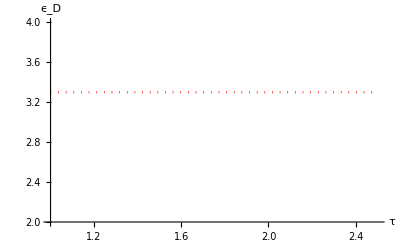

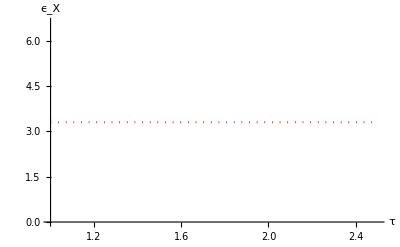

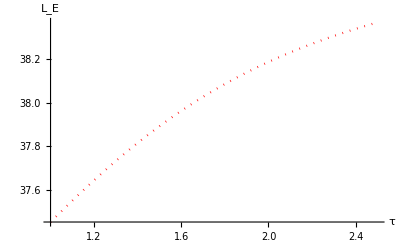

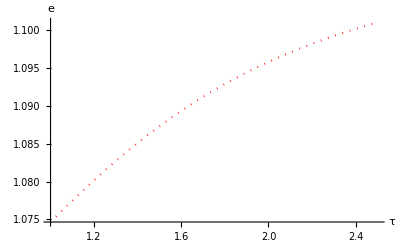

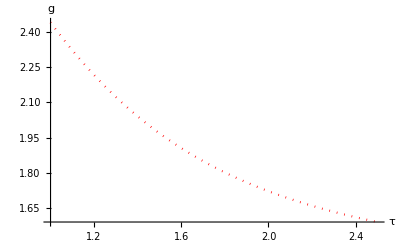

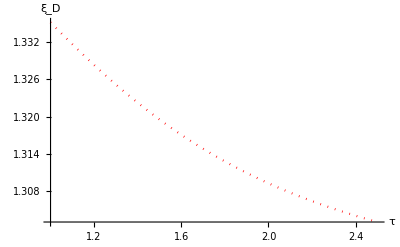

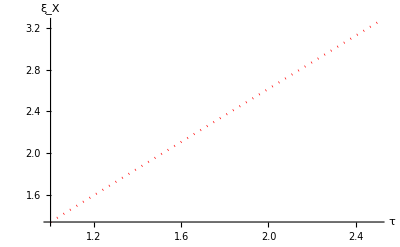

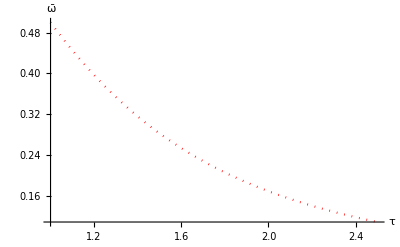

-Graphics-

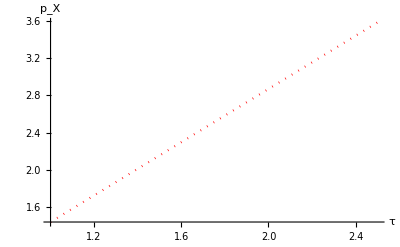

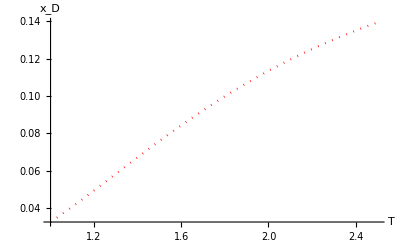

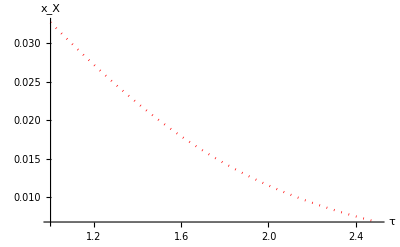

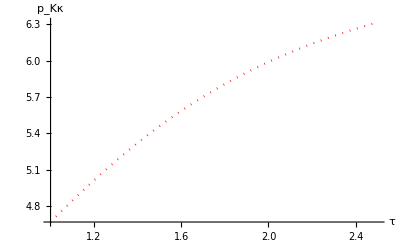

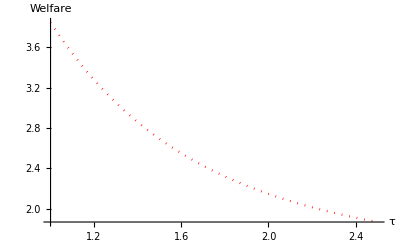

```mathematica
CEStauCH1=Plot[Subscript[ϵ, D]/.parameters/.
FindRoot[{neweqn1L,neweqn2L,neweqn3L,neweqn4L,neweqn5L,neweqn6L,neweqn7L,neweqn8L},{{Subscript[ξ, D],0.5},{Subscript[ξ, X],0.6},{ε̃,1.5},{ω̃,0.6},{g,0.8},{e,1},{Le,20},{Subscript[p, K],0.7}}],{τ,1,2.5},PlotRange->{{1,2.5},{2,4}},PlotStyle-> {Red,Dotted},AxesLabel-> {τ,"ϵ_D" }]
CEStauCH2=Plot[Subscript[ϵ, X]/.parameters/.
FindRoot[{neweqn1L,neweqn2L,neweqn3L,neweqn4L,neweqn5L,neweqn6L,neweqn7L,neweqn8L},{{Subscript[ξ, D],0.5},{Subscript[ξ, X],0.6},{ε̃,1.5},{ω̃,0.6},{g,0.8},{e,1},{Le,20},{Subscript[p, K],0.7}}],{τ,1,2.5},PlotStyle-> {Red,Dotted},AxesLabel-> {τ,"ϵ_X" }]
CEStauCH3=Plot[Le/.FindRoot[{neweqn1L,neweqn2L,neweqn3L,neweqn4L,neweqn5L,neweqn6L,neweqn7L,neweqn8L},{{Subscript[ξ, D],0.5},{Subscript[ξ, X],0.6},{ε̃,1.5},{ω̃,0.6},{g,0.8},{e,1},{Le,20},{Subscript[p, K],0.7}}],{τ,1,2.5},PlotStyle-> {Red,Dotted},AxesLabel-> {τ,"L_E" }]
CEStauCH4=Plot[e/.FindRoot[{neweqn1L,neweqn2L,neweqn3L,neweqn4L,neweqn5L,neweqn6L,neweqn7L,neweqn8L},{{Subscript[ξ, D],0.5},{Subscript[ξ, X],0.6},{ε̃,1.5},{ω̃,0.6},{g,0.8},{e,1},{Le,20},{Subscript[p, K],0.7}}],{τ,1,2.5},PlotStyle-> {Red,Dotted},AxesLabel-> {τ,"e" }]
CEStauCH5=Plot[g/.FindRoot[{neweqn1L,neweqn2L,neweqn3L,neweqn4L,neweqn5L,neweqn6L,neweqn7L,neweqn8L},{{Subscript[ξ, D],0.5},{Subscript[ξ, X],0.6},{ε̃,1.5},{ω̃,0.6},{g,0.8},{e,1},{Le,20},{Subscript[p, K],0.7}}],{τ,1,2.5},PlotStyle-> {Red,Dotted},AxesLabel-> {τ,"g" }]
CEStauCH6=Plot[Subscript[ξ, D]/.FindRoot[{neweqn1L,neweqn2L,neweqn3L,neweqn4L,neweqn5L,neweqn6L,neweqn7L,neweqn8L},{{Subscript[ξ, D],0.5},{Subscript[ξ, X],0.6},{ε̃,1.5},{ω̃,0.6},{g,0.8},{e,1},{Le,20},{Subscript[p, K],0.7}}],{τ,1,2.5},PlotStyle-> {Red,Dotted},AxesLabel-> {τ,"ξ_D" }]
CEStauCH7=Plot[Subscript[ξ, X]/.FindRoot[{neweqn1L,neweqn2L,neweqn3L,neweqn4L,neweqn5L,neweqn6L,neweqn7L,neweqn8L},{{Subscript[ξ, D],0.5},{Subscript[ξ, X],0.6},{ε̃,1.5},{ω̃,0.6},{g,0.8},{e,1},{Le,20},{Subscript[p, K],0.7}}],{τ,1,2.5},PlotStyle-> {Red,Dotted},AxesLabel-> {τ,"ξ_X" }]
CEStauCH8=Plot[ω̃/.FindRoot[{neweqn1L,neweqn2L,neweqn3L,neweqn4L,neweqn5L,neweqn6L,neweqn7L,neweqn8L},{{Subscript[ξ, D],0.5},{Subscript[ξ, X],0.6},{ε̃,1.5},{ω̃,0.6},{g,0.8},{e,1},{Le,20},{Subscript[p, K],0.7}}],{τ,1,2.5},PlotStyle-> {Red,Dotted},AxesLabel-> {τ,"ω̄" }]
CEStauCH9=Plot[ε̃/.FindRoot[{neweqn1L,neweqn2L,neweqn3L,neweqn4L,neweqn5L,neweqn6L,neweqn7L,neweqn8L},{{Subscript[ξ, D],0.5},{Subscript[ξ, X],0.6},{ε̃,1.5},{ω̃,0.6},{g,0.8},{e,1},{Le,20},{Subscript[p, K],0.7}}],{τ,1,2.5},PlotStyle-> {Red,Dotted},AxesLabel-> {τ,"ϵ̄" }]
CEStauCH10=Plot[Subscript[ξ, D] e/.FindRoot[{neweqn1L,neweqn2L,neweqn3L,neweqn4L,neweqn5L,neweqn6L,neweqn7L,neweqn8L},{{Subscript[ξ, D],0.5},{Subscript[ξ, X],0.6},{ε̃,1.5},{ω̃,0.6},{g,0.8},{e,1},{Le,20},{Subscript[p, K],0.7}}],{τ,1,2.5},PlotStyle-> {Red,Dotted},AxesLabel-> {τ,"p_D" }]
CEStauCH11=Plot[Subscript[ξ, X] e/.FindRoot[{neweqn1L,neweqn2L,neweqn3L,neweqn4L,neweqn5L,neweqn6L,neweqn7L,neweqn8L},{{Subscript[ξ, D],0.5},{Subscript[ξ, X],0.6},{ε̃,1.5},{ω̃,0.6},{g,0.8},{e,1},{Le,20},{Subscript[p, K],0.7}}],{τ,1,2.5},PlotStyle-> {Red,Dotted},AxesLabel-> {τ,"p_X" }]
CEStauCH12=Plot[v'[Subscript[ξ, D]]/muvalue/.parameters/.FindRoot[{neweqn1L,neweqn2L,neweqn3L,neweqn4L,neweqn5L,neweqn6L,neweqn7L,neweqn8L},{{Subscript[ξ, D],0.5},{Subscript[ξ, X],0.6},{ε̃,1.5},{ω̃,0.6},{g,0.8},{e,1},{Le,20},{Subscript[p, K],0.7}}],{τ,1,2.5},PlotStyle-> {Red,Dotted},AxesLabel-> {T,"x_D"}]
CEStauCH13=Plot[v'[Subscript[ξ, X]]/muvalue/.parameters/.FindRoot[{neweqn1L,neweqn2L,neweqn3L,neweqn4L,neweqn5L,neweqn6L,neweqn7L,neweqn8L},{{Subscript[ξ, D],0.5},{Subscript[ξ, X],0.6},{ε̃,1.5},{ω̃,0.6},{g,0.8},{e,1},{Le,20},{Subscript[p, K],0.7}}],{τ,1,2.5},PlotStyle-> {Red,Dotted},AxesLabel-> {τ,"x_X"} ]
CEStauCH14=Plot[κ/(1+ω̃)/.parameters /.FindRoot[{neweqn1L,neweqn2L,neweqn3L,neweqn4L,neweqn5L,neweqn6L,neweqn7L,neweqn8L},{{Subscript[ξ, D],0.5},{Subscript[ξ, X],0.6},{ε̃,1.5},{ω̃,0.6},{g,0.8},{e,1},{Le,20},{ Subscript[p, K],0.7}}],{τ,1,2.5},PlotStyle-> {Red,Dotted},AxesLabel-> {τ,"p_Kκ"}]
CEStauCH15=Plot[1/ρ(Log[v[Subscript[ξ, D]]+v[Subscript[ξ, X]]]+ g/ρ)/.parameters /.FindRoot[{neweqn1L,neweqn2L,neweqn3L,neweqn4L,neweqn5L,neweqn6L,neweqn7L,neweqn8L},{{Subscript[ξ, D],0.5},{Subscript[ξ, X],0.6},{ε̃,1.5},{ω̃,0.6},{g,0.8},{e,1},{Le,20},{ Subscript[p, K],0.7}}],{τ,1,2.5},PlotStyle-> {Red,Dotted},AxesLabel-> {τ,Welfare} ]
```

```mathematica
allCEStauCH={{CEStauCH1,CEStauCH2,CEStauCH3,CEStauCH4},{CEStauCH5,CEStauCH6,CEStauCH7,CEStauCH8},{CEStauCH9,CEStauCH10,CEStauCH11,CEStauCH12},{CEStauCH13,CEStauCH14,CEStauCH15}}
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-}}